## Projection of Phase Diagram

```mathematica
Clear["Global`*"]
```

```mathematica
ham[Δ_,Ω_,γ_]:=Evaluate[{{Δ-I γ,1,Ω/2},{1,Δ+I γ,Ω/2},{Ω/2,Ω/2,0}}];
ham[Δ,Ω,γ]//MatrixForm
disc[Δ_,Ω_,γ_]:=Evaluate[Discriminant[Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]]
Simplify[Expand[Simplify[disc[Δ,Ω,γ]]]-Expand[Simplify[disc[-Δ,Ω,γ]]]]
Collect[Det[IdentityMatrix[3]e-ham[Δ,Ω,γ]],e]
```

(-ⅈ γ+Δ | 1 | Ω/2
1 | ⅈ γ+Δ | Ω/2
Ω/2 | Ω/2 | 0)

Δ Ω^2 (36 γ^2+4 Δ^2+9 (-4+Ω^2))

e^3-2 e^2 Δ-Ω^2/2+(Δ Ω^2)/2+e (-1+γ^2+Δ^2-Ω^2/2)

```mathematica
EP2Surf[Δ_,Ω_,γ_]:=Simplify[Discriminant[Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]]
EP2Surf[Δ,Ω,γ]
```

-4 γ^6+1/4 (-4+4 Δ+Ω^2)^2 (1+2 Δ+Δ^2+2 Ω^2)+γ^4 (-8 Δ^2+6 (2+Ω^2))-γ^2 (4 Δ^4-18 Δ Ω^2+3 (2+Ω^2)^2+2 Δ^2 (-8+5 Ω^2))

```mathematica
Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,0];
ReEquSurf=Numerator@Simplify[(a1-3a0/a2)/2-(a2/3)^2]
```

e^3-2 e^2 Δ-Ω^2/2+(Δ Ω^2)/2+e (-1+γ^2+Δ^2-Ω^2/2)

4 Δ^3-27 Ω^2+9 Δ (-4+4 γ^2+Ω^2)

```mathematica
EP3EqG=FactorList[Simplify[Resultant[EP2Surf[Δ,Ω,γ],ReEquSurf,γ]]];
EP3G0=FactorList[EP2Surf[Δ,Ω,0]];
EP3ProjLineG=EP3EqG[[2,1]];
EP3EqG//MatrixForm
EP3G0//MatrixForm
```

(16 | 1
16 Δ^3-27 Ω^2+27 Δ Ω^2 | 6)

(4 | -1
-4+4 Δ+Ω^2 | 2
1+2 Δ+Δ^2+2 Ω^2 | 1)

```mathematica
P2=Show[ContourPlot[{EP3ProjLineG==0,EP3G0[[2,1]]==0},{Δ,-0.3,1.2},{Ω,0,3},PlotPoints->50,ContourStyle->{{RGBColor[.8,0,0,1],Thickness[0.01]},{RGBColor[0,.3,.7,1],Thickness[0.01]}}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{-0.3,0},{1.5,0}}]}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{0,0},{0,3.02}}]}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{1.01,0},{1.01,3.02}}]}]];
```

```mathematica
P3=Show[
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG>0&&Ω>0,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.5]}],
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG>0&&Δ<1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.3]}],
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG<0&&0<Δ<1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.5]}],
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG<0&&0<Δ<1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.3]}],
RegionPlot[EP3G0[[2,1]]>0&&Δ<0,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.45]}],
RegionPlot[EP3G0[[2,1]]<0&&Δ<0,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.7,0,.6]}],
RegionPlot[Δ>1,{Δ,-0.3,1.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{Darker@Cyan,Opacity[.5](*,GrayLevel[0.75]*)}],
P2,Frame->True,FrameLabel->{"Δ/C","Ω/C"},PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,0.5,1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-0.3,1.3},{0,3}},ImageSize->300];
```

## 2D Ω slice cut

```mathematica
Ω0=(*12/8*)(*3/5*)(*5/2*)(*3*)3/5
```

3/5

```mathematica
cs1=Flatten[Δ/.Solve[(-4+4 Δ+Ω^2/.Ω->Ω0)==0,Δ]][[1]]
cs2=Flatten[Δ/.Solve[(16 Δ^3-27 Ω^2+27 Δ Ω^2/.Ω->Ω0)==0,Δ]][[1]]
```

91/100

Root0.616Root[-243+243 #1+400 #1^3&,1]0.6157336413227936

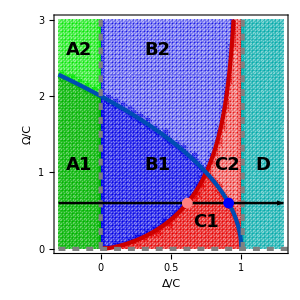

```mathematica
P4=Show[P3,With[{Ω=Ω0},Graphics[{Black,Thickness[0.006],Arrow[{{-0.3,Ω},{1.3,Ω}}]}]],With[{Δ=cs1},Graphics[{Dashed,Blue,PointSize[0.025],Point[{{cs1,Ω0},{cs1,Ω0}}]}]],With[{Δ=cs2},Graphics[{Dashed,Pink,PointSize[0.025],Point[{{cs2,Ω0},{cs2,Ω0}}]}]],
Graphics[{Text[Style["A1",FontFamily->"Arial",Bold,18],{-0.15,1.1}]}],Graphics[{Text[Style["A2",FontFamily->"Arial",Bold,18],{-0.15,2.6}]}],
Graphics[{Text[Style["B1",FontFamily->"Arial",Bold,18],{0.4,1.1}]}],Graphics[{Text[Style["B2",FontFamily->"Arial",Bold,18],{0.4,2.6}]}],Graphics[{Text[Style["C1",FontFamily->"Arial",Bold,18],{0.75,0.35}]}],Graphics[{Text[Style["C2",FontFamily->"Arial",Bold,18],{0.9,1.1}]}],Graphics[{Text[Style["D",FontFamily->"Arial",Bold,18],{1.15,1.1}]}]]
```

```mathematica
PhaseCut=Simplify[Discriminant[Det[ham[Δ,Ω0,γ]-IdentityMatrix[3]e],e]]
```

-4 γ^6+γ^4 (354/25-8 Δ^2)+((91-100 Δ)^2 (43+50 Δ+25 Δ^2))/62500+γ^2 (-10443/625+(162 Δ)/25+(62 Δ^2)/5-4 Δ^4)

```mathematica
Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,0];
realcond=(a1-3a0/a2)/2-(a2/3)^2/.{Ω->Ω0}
```

e^3-2 e^2 Δ-Ω^2/2+(Δ Ω^2)/2+e (-1+γ^2+Δ^2-Ω^2/2)

-(4 Δ^2)/9+1/2 (-59/50+γ^2-(3 (9/50-(9 Δ)/50))/(2 Δ)+Δ^2)

```mathematica
gs=γ/.Solve[(realcond/.{Δ->cs2})==0,γ][[2]]
```

1/30 √((243+819 Root0.616Root[-243+243 #1+400 #1^3&,1]0.6157336413227936-100 (Root0.616Root[-243+243 #1+400 #1^3&,1]0.6157336413227936)^3)/(Root0.616Root[-243+243 #1+400 #1^3&,1]0.6157336413227936))

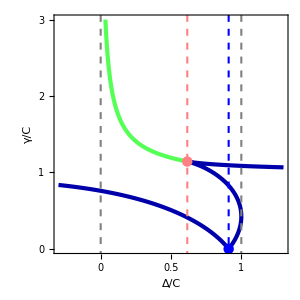

```mathematica
P5=Show[ContourPlot[PhaseCut==0,{Δ,-0.3,1.3},{γ,0,3},PlotPoints->100,ContourStyle->Directive[Darker@Blue,Opacity[1],Thickness[0.01]]],
ContourPlot[realcond==0,{Δ,0,cs2},{γ,0,3},PlotPoints->100,ContourStyle->Directive[Lighter@Green,Opacity[1],Thickness[0.01]]],
Graphics[{Dashed,Thickness[0.005],Gray,Line[{{0,-0.3},{0,3.3}}],Line[{{1,-0.3},{1,3.3}}]}],
With[{Δ=cs1},Graphics[{Dashed,Blue,PointSize[0.025],Point[{{cs1,0}}]}]],
Graphics[{Blue,Dashed,Thickness[0.005],Line[{{cs1,-0.3},{cs1,3.3}}]}],With[{Δ=cs2},Graphics[{Dashed,Pink,PointSize[0.025],Point[{{cs2,N[gs]}}]}]],Graphics[{Pink,Dashed,Thickness[0.005],Line[{{cs2,-0.3},{cs2,3.3}}]}],
Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,0.5,1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-0.3,1.3},{0,3}},ImageSize->300,FrameLabel->{"Δ/C","γ/C"}]
```

```mathematica
P6=Show[RegionPlot[-0.3<Δ<0,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.7,0,.6]}],RegionPlot[-0<Δ<cs2,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.5]}],RegionPlot[cs2<Δ<cs1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.5]}],RegionPlot[cs1<Δ<1,{Δ,-0.3,1.2},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.3]}],RegionPlot[Δ>1,{Δ,-0.3,1.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{Darker@Cyan,Opacity[.5]}],P5,Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,0.5,1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-0.3,1.3},{0,3}},ImageSize->300,FrameLabel->{"Δ/C","γ/C"}];
```

## Eigenvalues in different regions

```mathematica
Clear[Δ,Ω,γ]
```

```mathematica
Ω0=3/5(*3/5*)(*3*)(*1*)(*3*);
Δ0=(*1.15*)0.8(*0.85*);
ham[Δ_,Ω_,γ_]:=Evaluate[{{Δ-I γ,1,Ω/2},{1,Δ+I γ,Ω/2},{Ω/2,Ω/2,0}}];
ham[Δ,Ω0,γ]//MatrixForm
```

(-ⅈ γ+Δ | 1 | 3/10
1 | ⅈ γ+Δ | 3/10
3/10 | 3/10 | 0)

```mathematica
γlist=Table[i,{i,0,2,0.001}];
γlists=Table[i,{i,1,2,0.001}];
```

```mathematica
eigbr1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re](*Eigenvalues[ham[Δ0,Ω0,#]]*)[[1]]}&/@γlist;
eigbr2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re](*Eigenvalues[ham[Δ0,Ω0,#]]*)[[2]]}&/@γlist;
eigbr3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re](*Eigenvalues[ham[Δ0,Ω0,#]]*)[[3]]}&/@γlist;
eigbrs1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[1]]}&/@γlists;
eigbrs2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[2]]}&/@γlists;
eigbrs3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[3]]}&/@γlists;
eigbi1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[1]]}&/@γlist;
eigbi2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[2]]}&/@γlist;
eigbi3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[3]]}&/@γlist;
eigbis1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[1]]}&/@γlists;
eigbis2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[2]]}&/@γlists;
eigbis3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[3]]}&/@γlists;
```

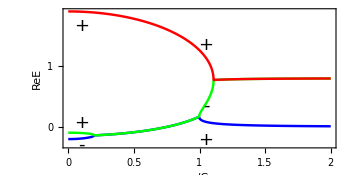

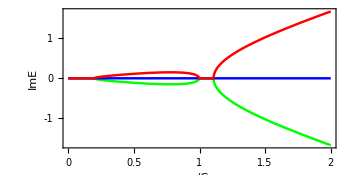

```mathematica
G1=Show[Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbr1]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbr2]}],
Graphics[{Red,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbr3]}],
(*Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbrs1]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbrs2]}],
Graphics[{Red,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbrs3]}],*)
Graphics[{Text[Style["+",FontFamily->"Arial",(*Bold,*)18],{0.1,1.65}]}],Graphics[{Text[Style["+",FontFamily->"Arial",(*Bold,*)18],{0.1,0.07}]}],Graphics[{Text[Style["-",FontFamily->"Arial",(*Bold,*)18],{0.1,-.3}]}],
Graphics[{Text[Style["+",FontFamily->"Arial",(*Bold,*)18],{1.05,1.35}]}],
Graphics[{Text[Style["-",FontFamily->"Arial",(*Bold,*)18],{1.05,0.35}]}],Graphics[{Text[Style["+",FontFamily->"Arial",(*Bold,*)18],{1.05,-.22}]}],
Graphics[{Text[Style["",FontFamily->"Arial",(*Bold,*)18],{0.1,-1}]}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{2,0,1,-1},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{"γ/C","ReE"},AspectRatio->1/2,ImageSize->{350,Automatic}]
G2=Show[Graphics[{Green,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbi1]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbi2]}],
Graphics[{Red,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbi3]}],
(*Graphics[{Red,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbis1]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbis2]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbis3]}],*)
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{-1,0,1},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{"γ/C","ImE"},AspectRatio->1/2,ImageSize->{350,Automatic}]
```

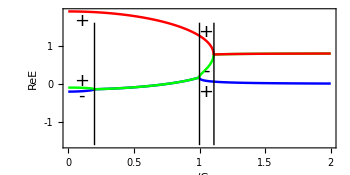

```mathematica
Show[G1,With[{x=0.2},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],With[{x=1},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],With[{x=1.11},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]]]
```

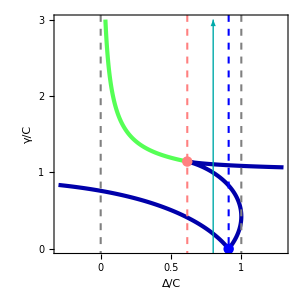

```mathematica
Show[P5,Graphics[{Darker@Cyan,Arrow[{{Δ0,-0.3},{Δ0,3}}]}]]
```

Parameters: 
Ω0/C=3/5;
Δ/C={-0.15,0.3,N@cs2,0.8,0.98,1.15}

## Parity indicator -1

```mathematica
γ0list=Table[i,{i,0,2,0.007}];
P={{0,1,0},{1,0,0},{0,0,1}};
abcr=Eigenvectors[ham[Δ0,Ω0,#]][[OrderingBy[Eigenvalues[ham[Δ0,Ω0,#]],Re[#]&]]]&/@γ0list;
abcl=Eigenvectors[Conjugate[ham[Δ0,Ω0,#]]][[OrderingBy[Eigenvalues[Conjugate[ham[Δ0,Ω0,#]]],Re[#]&]]]&/@γ0list;
Length@γ0list
```

286

```mathematica
er1=abcr[[;;,1]];
el1=abcl[[;;,1]];
er2=abcr[[;;,2]];
el2=abcl[[;;,2]];
er3=abcr[[;;,3]];
el3=abcl[[;;,3]];
```

```mathematica
ϵ1list=ParallelTable[{γ0list[[i]],(Conjugate[el1[[i]]].P.er1[[i]])/(Conjugate[el1[[i]]].er1[[i]])/Abs[(Conjugate[el1[[i]]].P.er1[[i]])/(Conjugate[el1[[i]]].er1[[i]])]},{i,1,Length@γ0list,1}];
```

```mathematica
ϵ2list=ParallelTable[{γ0list[[i]],(Conjugate[el2[[i]]].P.er2[[i]])/(Conjugate[el2[[i]]].er2[[i]])/Abs[(Conjugate[el2[[i]]].P.er2[[i]])/(Conjugate[el2[[i]]].er2[[i]])]},{i,1,Length@γ0list,1}];
```

```mathematica
ϵ3list=ParallelTable[{γ0list[[i]],(Conjugate[el3[[i]]].P.er3[[i]])/(Conjugate[el3[[i]]].er3[[i]])/Abs[(Conjugate[el3[[i]]].P.er3[[i]])/(Conjugate[el3[[i]]].er3[[i]])]},{i,1,Length@γ0list,1}];
```

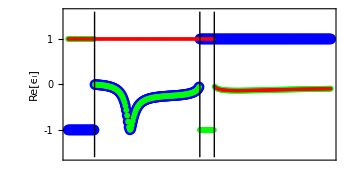

```mathematica
Show[ListPlot[{#[[1]],Re[#[[2]]]}&/@ϵ1list,PlotStyle->{Blue,PointSize[0.022]},PlotRange->All],ListPlot[{#[[1]],Re[#[[2]]]}&/@ϵ2list,PlotStyle->{Green,PointSize[0.012]},PlotRange->All],ListPlot[{#[[1]],Re[#[[2]]]}&/@ϵ3list,PlotStyle->{Red,PointSize[0.007]},PlotRange->All],With[{x=0.2},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],With[{x=1},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],With[{x=1.11},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{-1,0,1},None},{None,None}},AspectRatio->1/2,ImageSize->{350,Automatic},FrameLabel->{(*"γ/C"*)None,"Re[ϵ_i]"}]
```

```mathematica
Show[G1,With[{x=0.2},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],With[{x=1},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],With[{x=1.11},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]]]
```

-Graphics-

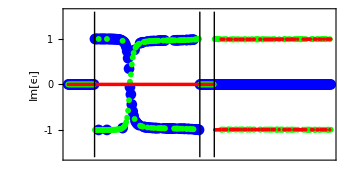

```mathematica
Show[ListPlot[{#[[1]],Im[#[[2]]]}&/@ϵ1list,PlotStyle->{Blue,PointSize[0.022]},PlotRange->All],ListPlot[{#[[1]],Im[#[[2]]]}&/@ϵ2list,PlotStyle->{Green,PointSize[0.012]},PlotRange->All],ListPlot[{#[[1]],Im[#[[2]]]}&/@ϵ3list,PlotStyle->{Red,PointSize[0.007]},PlotRange->All],With[{x=0.2},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],With[{x=1},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],With[{x=1.11},Graphics[{Line[{{x,-1.6},{x,1.6}}]}]],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{-1,0,1},None},{None(*{0,0.5,1,1.5,2}*),None}},AspectRatio->1/2,ImageSize->{350,Automatic},FrameLabel->{None(*"γ/C"*),"Im[ϵ_i]"}]
```

```mathematica
Table[Conjugate[er1[[i]]].er1[[i]],{i,1,Length@er1}];
Table[Conjugate[el1[[i]]].el1[[i]],{i,1,Length@el1}];
```